```mathematica
Quiet[Remove["Global`*"]];
ass = {x0∈Reals&&y0∈Reals&&k1>0&&k2>0&&dx0>0&&dy0>0&&dk1>0&&dk2>0&&s1>0&&s2>0&&x1∈Reals&&x2∈Reals&&x2>x1&&y1>0&&y2>y1};
g[y_, y0_, s2_]:=Exp[-(y-y0)^2/2/s2]/Sqrt[2*Pi*s2];
r[x_, y_, x0_, y0_, k_,dx0_, dy0_, dk_]:=g[y, y0+k*(x-x0), k^2*x^2+dy0^2+k^2*dx0^2+x0^2*dk^2];
r1[x_, y_, x0_, y0_, k1_,dx0_, dy0_, dk1_]:=r[x, y,x0,y0,k1,dx0,dy0,dk1];
r2[x_, y_, x0_, y0_, k2_,dx0_, dy0_, dk2_]:=r[x, y,x0,y0,k2,dx0,dy0,dk2];re[a_, ye_, y_]:=g[y, ye, (a*ye)^2];
a1[a_, x_, y_, x0_, y0_, k1_, dx0_, dy0_, dk1_,y1_,y2_]:=Integrate[r1[x, yy,x0,y0,k1,dx0,dy0,dk1]*re[a, y, yy],{yy, y1, y2},Assumptions->ass];
a2[a_, x_, y_, x0_, y0_, k2_, dx0_, dy0_, dk2_,y1_,y2_]:=Integrate[r2[x, yy,x0,y0,k2,dx0,dy0,dk2]*re[a, y, yy],{yy, y1,y2},Assumptions->ass];
h[x_, y_, s1_, s2_, x0_, y0_, k1_, k2_]:=g[y, y0+k1*(x-x0), (s1*y)^2]+g[y, y0+k2*(x-x0), (s2*y)^2];
z[x1_, x2_,s1_, s2_, x0_, y0_, k1_, k2_,y1_,y2_]:= Integrate[h[x, y, s1, s2, x0, y0, k1, k2],{x,x1,x2}, {y,y1,y2},Assumptions->ass];
p[a_, x1_, x2_, s1_, s2_, x0_, y0_, k1_, k2_, dx0_, dy0_, dk1_, dk2_,y1_,y2_]:= Integrate[h[x, y, s1, s2, x0, y0, k1, k2]*Abs[a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,y1,y2] - a2[a, x, y, x0, y0, k2, dx0, dy0, dk2,y1,y2]]/(a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,y1,y2]+a2[a, x, y, x0, y0, k2, dx0, dy0, dk2,y1,y2]),{x,x1,x2},{y,y1,y2},Assumptions->ass]/z[x1, x2,s1, s2, x0, y0, k1, k2,y1,y2];
```

```mathematica
aa1=FullSimplify[a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,-Infinity,Infinity]];
Print[aa1]
```

$Aborted

aa1

```mathematica
Quiet[Remove["Global`*"]];
g[y_, y0_, s2_]:=Exp[-N[(y-y0)^2/2/s2]]/Sqrt[2*Pi*s2];
r[x_, y_, x0_, y0_, k_,dx0_, dy0_, dk_]:=g[y, y0+k*(x-x0), k^2*x^2+dy0^2+k^2*dx0^2+x0^2*dk^2];
r1[x_, y_, x0_, y0_, k1_,dx0_, dy0_, dk1_]:=r[x, y,x0,y0,k1,dx0,dy0,dk1];
r2[x_, y_, x0_, y0_, k2_,dx0_, dy0_, dk2_]:=r[x, y,x0,y0,k2,dx0,dy0,dk2];re[a_, ye_, y_]:=g[y, ye, (a*ye)^2];
a1[a_, x_, y_, x0_, y0_, k1_, dx0_, dy0_, dk1_,y1_,y2_]:=NIntegrate[r1[x, yy,x0,y0,k1,dx0,dy0,dk1]*re[a, y, yy],{yy, y1, y2}];
a2[a_, x_, y_, x0_, y0_, k2_, dx0_, dy0_, dk2_,y1_,y2_]:=NIntegrate[r2[x, yy,x0,y0,k2,dx0,dy0,dk2]*re[a, y, yy],{yy, y1, y2}];
h[x_, y_, s1_, s2_, x0_, y0_, k1_, k2_]:=g[y, y0+k1*(x-x0), (s1*y)^2]+g[y, y0+k2*(x-x0), (s2*y)^2];
z[x1_, x2_,s1_, s2_, x0_, y0_, k1_, k2_,y1_,y2_]:= NIntegrate[h[x, y, s1, s2, x0, y0, k1, k2],{x,x1,x2}, {y,y1, y2}];
p[a_, x1_, x2_, s1_, s2_, x0_, y0_, k1_, k2_, dx0_, dy0_, dk1_, dk2_,y1_,y2_]:= NIntegrate[h[x, y, s1, s2, x0, y0, k1, k2]*Abs[a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,y1,y2] - a2[a, x, y, x0, y0, k2, dx0, dy0, dk2,y1,y2]]/(a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,y1,y2]+a2[a, x, y, x0, y0, k2, dx0, dy0, dk2,y1,y2]),{x,x1,x2},{y,y1,y2}]/z[x1, x2,s1, s2, x0, y0, k1, k2,y1,y2];
p1[a_, x_, y_, x0_, y0_, k1_, k2_, dx0_, dy0_, dk1_, dk2_,y1_,y2_]:=Module[{b1 = a1[a, x, y, x0, y0, k1, dx0, dy0, dk1,y1,y2], b2 = a2[a, x, y, x0, y0, k2, dx0, dy0, dk2,y1,y2]},b1/(b1+b2)]
pmax[a_, x_, y_, x0_, y0_, k1_, k2_, dx0_, dy0_, dk1_, dk2_,y1_,y2_]:=Module[{pp1=p1[a, x, y, x0, y0, k1, k2, dx0, dy0, dk1, dk2,y1,y2]},Max[pp1, 1-pp1]]
plog[mx_,a_, x_, y_, x0_, y0_, k1_, k2_, dx0_, dy0_, dk1_, dk2_,y1_,y2_]:=Module[{pp1=p1[a, x, y, x0, y0, k1, k2, dx0, dy0, dk1, dk2,y1,y2]},Min[Abs[Log10[1/pp1-1]],Log10[mx]]]
```

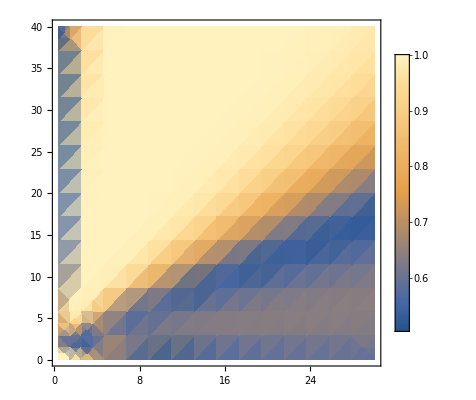

```mathematica
x0 = 0.4;
y0 = 2;
x1=x0;
x2=30;
y1=0.1;
y2=40;
k1=0.25;
k2=0.4;
dk1=0.0025;
dk2=0.004;
dx0=0.001;
dy0=0.001;
s1=0.1;
s2=0.1;
mx=10;

xarg=1;
yarg=5.8;
aarg=0.1;

DensityPlot[pmax[aarg, x, y, x0, y0, k1, k2, dx0, dy0, dk1, dk2,y1,y2],{x,x1,x2},{y,y1,y2},PlotLegends->Automatic](*DensityPlot[plog[mx,aarg, x, y, x0, y0, k1, k2, dx0, dy0, dk1, dk2,y1,y2],{x,x1,x2},{y,y1,y2},PlotLegends->Automatic]

Print["z:",z[x1, x2,s1, s2, x0, y0, k1, k2]];
Print["h[x,y]:",h[x, y, s1, s2, x0, y0, k1, k2]];
Print["a1[x,y]:",a1[a, x, y, x0, y0, k1, dx0, dy0, dk1]];
Print["a2[x,y]:",a2[a, x, y, x0, y0, k2, dx0, dy0, dk2]];
p[aarg, x1,x2,s1,s2,x0,y0, k1,k2,dx0, dy0, dk1, dk2,y1,y2]*)
```